```mathematica
ClearAll;
$Assumptions=A∈Integers&&A>2&&a∈Reals&&a>0&&Λ∈Reals&&Λ>0&&R∈Reals&&r∈Reals;
```

### LECs definition

```mathematica
λc={1,2,4,6,8,10,20};
CC={0.548,0.179,10.278,44.570,126.359,301.349,15229.622};
λd={2,4,6,8,10};
DD={7.749,194.253,4273.294,122391.358,4102409.239};
```

{cpol[1]→-303.928,cpol[2]→305.998,cpol[3]→-70.9796,cpol[4]→4.72532}

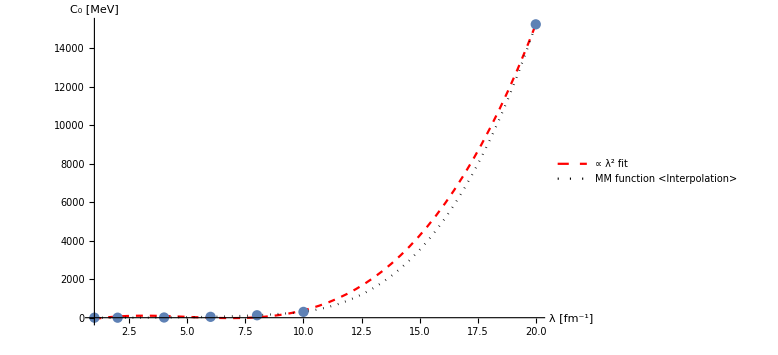

```mathematica
Clear[CL,CL2];
ord=3;
coeffsc=Array[cpol,ord+1];
modelc=Sum[coeffsc[[n+1]] l^n,{n,0,ord}];
lcfit=FindFit[Transpose[{λc,CC}],{modelc(*,Table[coeffs[[n]],{n,1,ord}]*)},coeffsc,l]
CL[ff_]:=modelc/.lcfit/.l->ff;
CL2=Interpolation[Transpose[{λc,CC}]];
Plot[{CL[x],CL2[x]},{x,Min[λc],Max[λc]},PlotStyle->{{Dashed,Red},{Black,Dotted}},AxesLabel->{"λ [fm^-1]","C_0 [MeV]"},PlotLegends->{"∝ λ^2 fit","MM function <Interpolation>"}];
Show[%,ListPlot[Transpose[{λc,CC}],PlotLegends->"calibration points"],ImageSize->Large]
```

{cpol[1]→306962.,cpol[2]→-245901.,cpol[3]→44319.3,cpol[4]→1921.75,cpol[5]→-361.152,cpol[6]→-58.3166,cpol[7]→-3.39616,cpol[8]→0.25108,cpol[9]→0.102293}

{cpol[1]→1.66832×10^6,cpol[2]→-1.56426×10^6,cpol[3]→425937.,cpol[4]→-22219.9,cpol[5]→-5081.17,cpol[6]→485.146}

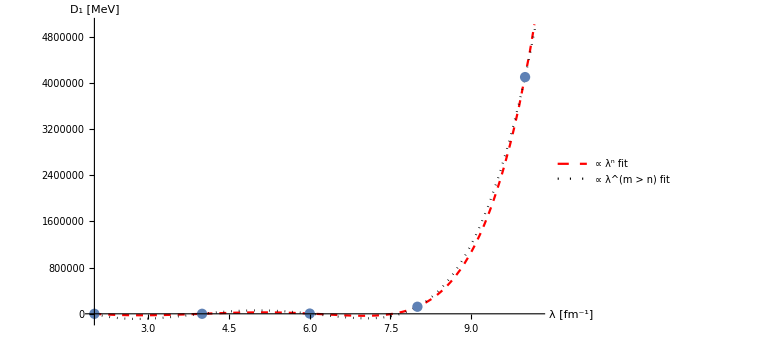

```mathematica
Clear[DL];
ord=8;
coeffsd=Array[cpol,ord+1];
modeld=Sum[coeffsd[[n+1]] l^n,{n,0,ord}];
ldfit=FindFit[Transpose[{λd,DD}],{modeld(*,Table[coeffs[[n]],{n,1,ord}]*)},coeffsd,l]
DL[ff_]:=modeld/.ldfit/.l->ff;
coeffs2=Array[cpol,6];
exp2={0,1,2,3,4,5};
model2=Sum[coeffs2[[n+1]] l^exp2[[n+1]],{n,0,5}];
ldfit2=FindFit[Transpose[{λd,DD}],{model2(*,Table[coeffs[[n]],{n,1,ord}]*)},coeffs2,l]
DL2[ff_]:=model2/.ldfit2/.l->ff;

Plot[{DL[x],DL2[x]},{x,Min[λd],1.1 Max[λd]},PlotStyle->{{Dashed,Red},{Black,Dotted}},AxesLabel->{"λ [fm^-1]","D_1 [MeV]"},PlotLegends->{"∝ λ^n fit","∝ λ^(m > n) fit"}];
Show[%,ListPlot[Transpose[{λd,DD}],PlotLegends->"calibration points"],ImageSize->Large,PlotRange->All]
```